## CP symmetry

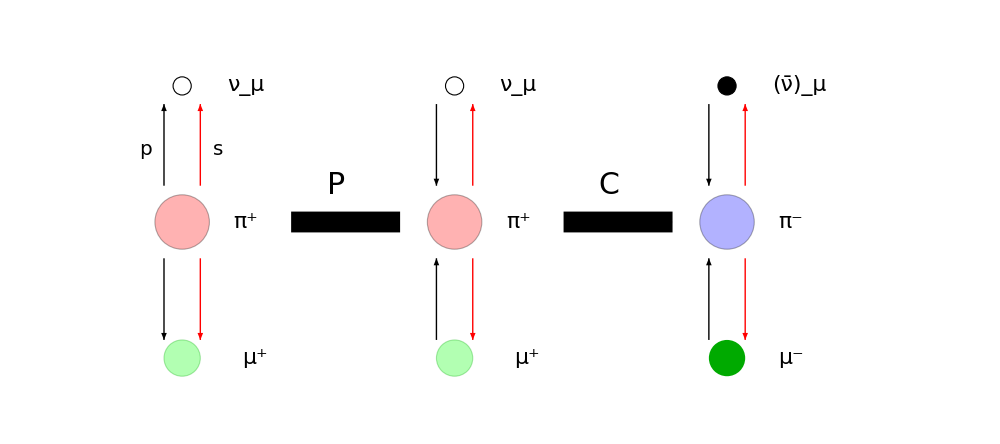

```mathematica
x1=0.5;
x2=2;
x3=3.5;
sp = 0.15;
sp1 = 0.05;
sp2 = 0.1;

pion = {Red,Opacity[0.3],EdgeForm[Directive[Thick,Dashed,Black]],Disk[{x1,0},sp],Disk[{x2,0},sp],Blue,Opacity[0.3],EdgeForm[Directive[Thick,Dashed,Black]],Disk[{x3,0},sp]};
muon = {{Green,Opacity[0.3],EdgeForm[Directive[Thick,Dashed,Darker[Green]]],Disk[{x1,-0.75},sp2],Disk[{x2,-0.75},sp2]},{Darker[Green],Disk[{x3,-0.75},sp2]}};
neutrino = {White,EdgeForm[Directive[Thick,Black]],Disk[{x1,0.75},sp1],Disk[{x2,0.75},sp1],Black,EdgeForm[Directive[Thick,Black]],Disk[{x3,0.75},sp1]};


parrow1 = {Black,Arrowheads[.02],Arrow[{{0.8x1,sp+0.05},{0.8x1,0.75-sp1-0.05}}],Arrow[{{x2-0.2x1,(0.75-sp1-0.05)},{x2-0.2x1,(sp+0.05)}}],Arrow[{{x3-0.2x1,(0.75-sp1-0.05)},{x3-0.2x1,(sp+0.05)}}]};
parrow2 = {Black,Arrowheads[.02],Arrow[{{0.8x1,-(sp+0.05)},{0.8x1,-(0.75-sp1-0.05)}}],Arrow[{{x2-0.2x1,-(0.75-sp1-0.05)},{x2-0.2x1,-(sp+0.05)}}],Arrow[{{x3-0.2x1,-(0.75-sp1-0.05)},{x3-0.2x1,-(sp+0.05)}}]};

sarrow1 = {Red,Arrowheads[.02],Arrow[{{1.2x1,sp+0.05},{1.2x1,0.75-sp1-0.05}}],Arrow[{{x2+0.2x1,(sp+0.05)},{x2+0.2x1,(0.75-sp1-0.05)}}],Arrow[{{x3+0.2x1,(sp+0.05)},{x3+0.2x1,(0.75-sp1-0.05)}}]};
sarrow2 = {Red,Arrowheads[.02],Arrow[{{1.2x1,-(sp+0.05)},{1.2x1,-(0.75-sp1-0.05)}}],Arrow[{{x2+0.2x1,-(sp+0.05)},{x2+0.2x1,-(0.75-sp1-0.05)}}],Arrow[{{x3+0.2x1,-(sp+0.05)},{x3+0.2x1,-(0.75-sp1-0.05)}}]};

text={{Text[Style["π^+",FontSize->22,FontFamily->"Palatino Linotype"],{x1+0.35,0}],Text[Style["π^+",FontSize->22,FontFamily->"Palatino Linotype"],{x2+0.35,0}],Text[Style["π^-",FontSize->22,FontFamily->"Palatino Linotype"],{x3+0.35,0}]},{Text[Style["ν_μ",FontSize->22,FontFamily->"Palatino Linotype"],{x1+0.35,0.75}],Text[Style["ν_μ",FontSize->22,FontFamily->"Palatino Linotype"],{x2+0.35,0.75}],Text[Style["(ν̄)_μ",FontSize->22,FontFamily->"Palatino Linotype"],{x3+0.4,0.75}]},{Text[Style["μ^+",FontSize->22,FontFamily->"Palatino Linotype"],{x1+0.4,-0.75}],Text[Style["μ^+",FontSize->22,FontFamily->"Palatino Linotype"],{x2+0.4,-0.75}],Text[Style["μ^-",FontSize->22,FontFamily->"Palatino Linotype"],{x3+0.35,-0.75}]},Text[Style["P",FontSize->30,FontFamily->"Palatino Linotype"],{x1+0.85,0.2}],Text[Style["C",FontSize->30,FontFamily->"Palatino Linotype"],{x2+0.85,0.2}],Text[Style["p",FontSize->20,FontFamily->"Palatino Linotype"],{0.3,0.4}],Text[Style["s",FontSize->20,FontFamily->"Palatino Linotype"],{0.7,0.4}]};

transformations={Black,Arrowheads[.07],Thickness[0.015],Arrow[{{x1+0.6,0},{x2-0.3,0}}],Arrow[{{x2+0.6,0},{x3-0.3,0}}]};

Graphics[{pion,muon,neutrino,parrow1,parrow2,sarrow1,sarrow2,text,transformations},PlotRange->{{0,4.5},{-1,1}},Axes->False,ImageSize->1000]
```

## ECL resolution

```mathematica
frame[legend_]:=Framed[legend,FrameStyle->Black,RoundingRadius->0,FrameMargins->0,Background->White]
sig[e_,a_]:=√((a 0.066)^2+(0.81/e^(1/4))^2*e^2+(1.34)^2*e^2)/e
```

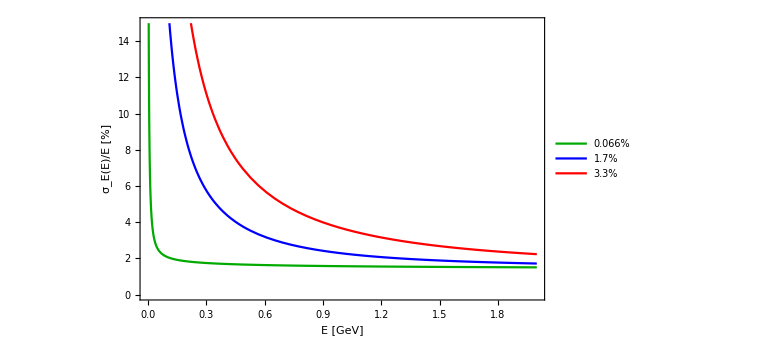

```mathematica
Plot[{sig[e,1],sig[e,25],sig[e,50]},{e,0,2},Frame->True,FrameStyle->Directive[Black,Large],Axes->False,ImageSize->Large, FrameLabel->{"E [GeV]","σ_E(E)/E [%]"},PlotStyle->{Darker[Green],Blue,Red},PlotLegends->Placed[LineLegend[{Darker[Green],Blue,Red},Table[Text[Style[ToString[NumberForm[a 0.066,2]]<>"%",FontSize->25]],{a,{1,25,50}}],LegendFunction->frame],{Right,Top}],PlotRange->{0,15}]
```

## ECL fit

{a→0.0170969,c→1.59073}

{a→1.89779,c→1.79343}

{a→1.99814,c→1.578}

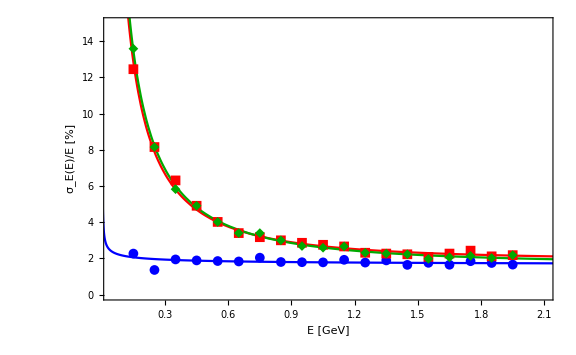

```mathematica
data=Import["D:\\Faks\\5. letnik\\Magisterij\\slike\\ECL_data.txt","Table"];
sig[e_,a_,b_,c_]:=√((a/e)^2+(b/e^(1/4))^2+(c)^2)

Clear[c];
b = 0.81;
model =√((a/e)^2+(b/e^(1/4))^2+(c)^2);

(*fit1 = NonlinearModelFit[{#[[1]],#[[2]]*100/2.355/#[[1]]}&/@data[[;;,{1,2}]],sig[x,a,0,c],{a,b,c},x]
fit2 = NonlinearModelFit[{#[[1]],#[[2]]*100/2.355/#[[1]]}&/@data[[;;,{1,3}]],sig[x,a,0,c],{a,b,c},x]
fit3 = NonlinearModelFit[{#[[1]],#[[2]]*100/2.355/#[[1]]}&/@data[[;;,{1,4}]],sig[x,a,0,c],{a,b,c},x]*)

fit1 = FindFit[{#[[1]],#[[2]]*100/2.355/#[[1]]}&/@data[[;;,{1,2}]],{model,{a>0,0.5<b<1.5,0<c<5}},{a,c},e]
fit2 = FindFit[{#[[1]],#[[2]]*100/2.355/#[[1]]}&/@data[[;;,{1,3}]],{model,{a>0,0.5<b<1.5,0<c<5}},{a,c},e]
fit3 = FindFit[{#[[1]],#[[2]]*100/2.355/#[[1]]}&/@data[[;;,{1,4}]],{model,{a>0,0.5<b<1.5,0<c<5}},{a,c},e]
(*

fit1["ParameterTable"]
fit2["ParameterTable"]
fit3["ParameterTable"]

p1=Plot[{fit1[e],fit2[e],fit3[e]},{e,0,2.3},Frame->True,FrameStyle->Directive[Black,Large],Axes->False,ImageSize->Large, FrameLabel->{"E [GeV]","σ_E(E)/E [%]"},PlotStyle->{Blue,Red,Darker[Green]},PlotRange->{0,150}];*)
p1=Plot[{model/.fit1,model/.fit2,model/.fit3},{e,0,2.3},Frame->True,FrameStyle->Directive[Black,Large],Axes->False,ImageSize->Large, FrameLabel->{"E [GeV]","σ_E(E)/E [%]"},PlotStyle->{Blue,Red,Darker[Green]},PlotRange->{0,150}];

p2=ListPlot[{{#[[1]],#[[2]]*100/2.355/#[[1]]}&/@data[[;;,{1,2}]],{#[[1]],#[[2]]*100/2.355/#[[1]]}&/@data[[;;,{1,3}]],{#[[1]],#[[2]]*100/2.355/#[[1]]}&/@data[[;;,{1,4}]]},ImageSize->Large,Frame->True,FrameStyle->Directive[Black,Large],PlotRange->All, FrameLabel->{"E [GeV]","σ_E(E)/E [%]"},PlotMarkers->{Automatic,10},PlotStyle->{Blue,Red,Darker[Green]}];

Show[{p1,p2},PlotRange->{{0.05,2.1},{0,15}}]
```

## Cluster

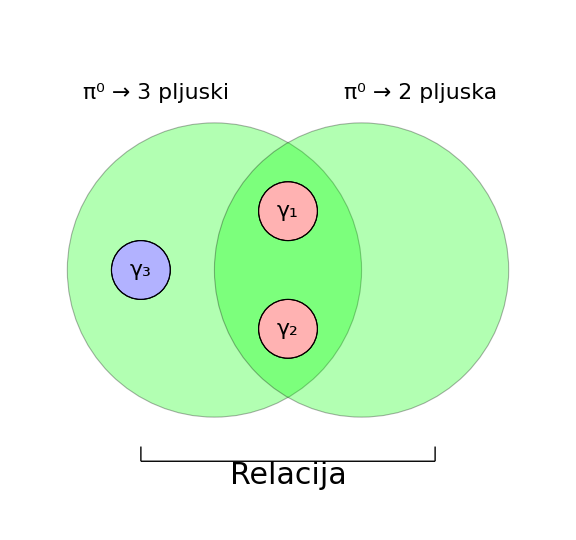

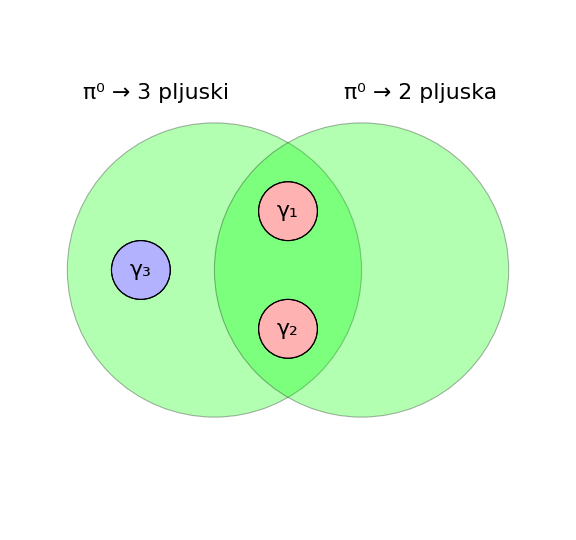

```mathematica
pi0={Green,Opacity[0.3],EdgeForm[Directive[Thick,Dashed,Black]],Disk[{1,0},0.5],Disk[{1.5,0},0.5]} ;
gamma = {White,Opacity[1],EdgeForm[Directive[Thick,Dashed,Black]],Disk[{1.25,0.2},0.1],Disk[{1.25,-0.2},0.1],Red,Opacity[0.3],Disk[{1.25,0.2},0.1],Disk[{1.25,-0.2},0.1],White,Opacity[1],Disk[{0.75,0},0.1],Blue,Opacity[0.3],Disk[{0.75,0},0.1]};
text = {Text[Style["π^0 → 3 pljuski",FontSize->22],{0.8,0.6}],Text[Style["π^0 → 2 pljuska",FontSize->22],{1.7,0.6}],Text[Style["γ_1",FontSize->22],{1.25,0.2}],Text[Style["γ_2",FontSize->22],{1.25,-0.2}],Text[Style["γ_3",FontSize->22],{0.75,0}],Text[Style["Relacija",FontSize->30],{1.25,-0.7}]};
line = {Thick,Line[{{0.75,-0.65},{0.75,-0.6}}],Line[{{1.75,-0.65},{1.75,-0.6}}],Line[{{0.75,-0.65},{1.75,-0.65}}]};


Graphics[{pi0,gamma,text,line},PlotRange->{{0.45,2.05},{-0.75,0.75}},Axes->False,ImageSize->Large]
pi0={Green,Opacity[0.3],EdgeForm[Directive[Thick,Dashed,Black]],Disk[{1,0},0.5],Disk[{1.5,0},0.5]} ;
gamma = {White,Opacity[1],EdgeForm[Directive[Thick,Dashed,Black]],Disk[{1.25,0.2},0.1],Disk[{1.25,-0.2},0.1],Red,Opacity[0.3],Disk[{1.25,0.2},0.1],Disk[{1.25,-0.2},0.1],White,Opacity[1],Disk[{0.75,0},0.1],Blue,Opacity[0.3],Disk[{0.75,0},0.1]};
text = {Text[Style["π^0 → 3 pljuski",FontSize->22],{0.8,0.6}],Text[Style["π^0 → 2 pljuska",FontSize->22],{1.7,0.6}],Text[Style["γ_1",FontSize->22],{1.25,0.2}],Text[Style["γ_2",FontSize->22],{1.25,-0.2}],Text[Style["γ_3",FontSize->22],{0.75,0}]};
line = {Thick,Line[{{0.75,-0.65},{0.75,-0.6}}],Line[{{1.75,-0.65},{1.75,-0.6}}],Line[{{0.75,-0.65},{1.75,-0.65}}]};


Graphics[{pi0,gamma,text},PlotRange->{{0.45,2.05},{-0.75,0.75}},Axes->False,ImageSize->Large]
```

## SM

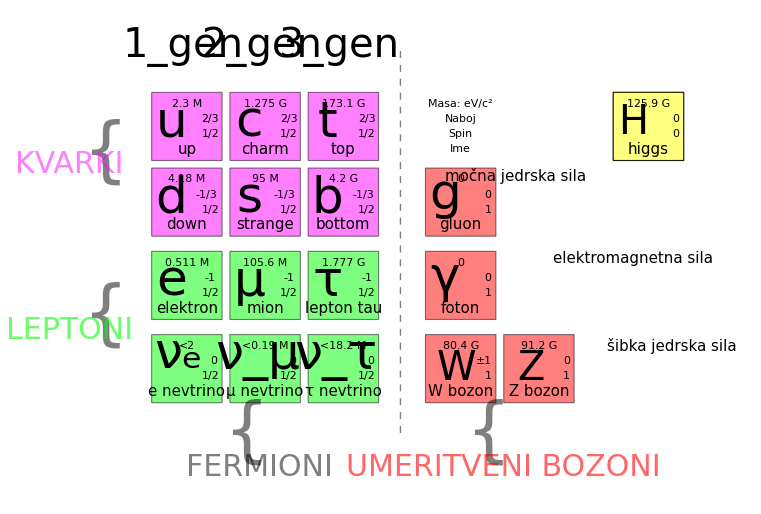

```mathematica
frame={{EdgeForm[{Black,Thick}],Yellow,Opacity[0],Rectangle[{-0.2,0.2},{7,-4-0.3},RoundingRadius->0.3]},
{EdgeForm[{Black,Thick}],Opacity[0],Rectangle[{-0.1,0.1},{6.5,-3-0.2},RoundingRadius->0.3]},
{EdgeForm[{Black,Thick}],Opacity[0],Rectangle[{0,0},{5,-2-0.1},RoundingRadius->0.3]}};

squares={{EdgeForm[{Black,Thick}],Magenta,Opacity[0.5],Rectangle[{0.1,-0.1},{1,-1},RoundingRadius->0.2]},{EdgeForm[{Black,Thick}],Magenta,Opacity[0.5],Rectangle[{1+0.1,-0.1},{1+1,-1},RoundingRadius->0.2]},{EdgeForm[{Black,Thick}],Magenta,Opacity[0.5],Rectangle[{2+0.1,-0.1},{2+1,-1},RoundingRadius->0.2]},

{EdgeForm[{Black,Thick}],Magenta,Opacity[0.5],Rectangle[{0.1,-1-0.1},{1,-1-1},RoundingRadius->0.2]},{EdgeForm[{Black,Thick}],Magenta,Opacity[0.5],Rectangle[{1+0.1,-1-0.1},{1+1,-1-1},RoundingRadius->0.2]},{EdgeForm[{Black,Thick}],Magenta,Opacity[0.5],Rectangle[{2+0.1,-1-0.1},{2+1,-1-1},RoundingRadius->0.2]},

{EdgeForm[{Black,Thick}],Green,Opacity[0.5],Rectangle[{0.1,-2-0.2},{1,-2-1-0.1},RoundingRadius->0.2]},{EdgeForm[{Black,Thick}],Green,Opacity[0.5],Rectangle[{1+0.1,-2-0.2},{1+1,-2-1-0.1},RoundingRadius->0.2]},{EdgeForm[{Black,Thick}],Green,Opacity[0.5],Rectangle[{2+0.1,-2-0.2},{2+1,-2-1-0.1},RoundingRadius->0.2]},

{EdgeForm[{Black,Thick}],Green,Opacity[0.5],Rectangle[{0.1,-3-0.3},{1,-3-1-0.2},RoundingRadius->0.2]},{EdgeForm[{Black,Thick}],Green,Opacity[0.5],Rectangle[{1+0.1,-3-0.3},{1+1,-3-1-0.2},RoundingRadius->0.2]},{EdgeForm[{Black,Thick}],Green,Opacity[0.5],Rectangle[{2+0.1,-3-0.3},{2+1,-3-1-0.2},RoundingRadius->0.2]},

{EdgeForm[{Black,Thick}],Opacity[0],Rectangle[{3.5+0.1,-0.1},{3.5+1,-1},RoundingRadius->0.2]},
{EdgeForm[{Black,Thick}],Red,Opacity[0.5],Rectangle[{3.5+0.1,-1-0.1},{3.5+1,-2},RoundingRadius->0.2]},
{EdgeForm[{Black,Thick}],Red,Opacity[0.5],Rectangle[{3.5+0.1,-2-0.2},{3.5+1,-3-0.1},RoundingRadius->0.2]},
{EdgeForm[{Black,Thick}],Red,Opacity[0.5],Rectangle[{3.5+0.1,-3-0.3},{3.5+1,-4-0.2},RoundingRadius->0.2]},
{EdgeForm[{Black,Thick}],Red,Opacity[0.5],Rectangle[{3.5+1+0.1,-3-0.3},{3.5+2,-4-0.2},RoundingRadius->0.2]},
{EdgeForm[{Black,Thick}],White,Opacity[1],Rectangle[{4.9+1+0.1,-0.1},{4.9+2,-1},RoundingRadius->0.2]},
{EdgeForm[{Black,Thick}],Yellow,Opacity[0.5],Rectangle[{4.9+1+0.1,-0.1},{4.9+2,-1},RoundingRadius->0.2]}};

name = {Text[Style["u",FontSize->50,FontFamily->"Times"],{0.35,-0.5}],
Text[Style["c",FontSize->50,FontFamily->"Times"],{1+0.35,-0.5}],
Text[Style["t",FontSize->50,FontFamily->"Times"],{2+0.35,-0.5}],
Text[Style["d",FontSize->50,FontFamily->"Times"],{0.35,-1-0.5}],
Text[Style["s",FontSize->50,FontFamily->"Times"],{1+0.35,-1-0.5}],
Text[Style["b",FontSize->50,FontFamily->"Times"],{2+0.35,-1-0.5}],

Text[Style["e",FontSize->50,FontFamily->"Times"],{0.35,-2-0.6}],
Text[Style["μ",FontSize->50,FontFamily->"Times"],{1+0.35,-2-0.6}],
Text[Style["τ",FontSize->50,FontFamily->"Times"],{2+0.35,-2-0.6}],
Text[Style["ν_e",FontSize->50,FontFamily->"Times"],{0.45,-3-0.55}],
Text[Style["ν_μ",FontSize->50,FontFamily->"Times"],{1+0.45,-3-0.6}],
Text[Style["ν_τ",FontSize->50,FontFamily->"Times"],{2+0.45,-3-0.6}],

Text[Style["g",FontSize->50,FontFamily->"Times"],{3.5+0.35,-1-0.45}],
Text[Style["γ",FontSize->50,FontFamily->"Times"],{3.5+0.35,-2-0.55}],
Text[Style["W",FontSize->40,FontFamily->"Times"],{3.5+0.5,-3-0.75}],
Text[Style["Z",FontSize->40,FontFamily->"Times"],{4.5+0.45,-3-0.75}],

Text[Style["H",FontSize->40,FontFamily->"Times"],{5.9+0.35,-0.5}]};

subname= {Text[Style["up",FontSize->15,FontFamily->"Times"],{0.55,-0.85}],
Text[Style["charm",FontSize->15,FontFamily->"Times"],{1+0.55,-0.85}],
Text[Style["top",FontSize->15,FontFamily->"Times"],{2+0.55,-0.85}],
Text[Style["down",FontSize->15,FontFamily->"Times"],{0.55,-1-0.85}],
Text[Style["strange",FontSize->15,FontFamily->"Times"],{1+0.55,-1-0.85}],
Text[Style["bottom",FontSize->15,FontFamily->"Times"],{2+0.55,-1-0.85}],

Text[Style["elektron",FontSize->15,FontFamily->"Times"],{0.55,-2-0.95}],
Text[Style["mion",FontSize->15,FontFamily->"Times"],{1+0.55,-2-0.95}],
Text[Style["lepton tau",FontSize->15,FontFamily->"Times"],{2+0.55,-2-0.95}],
Text[Style["e nevtrino",FontSize->15,FontFamily->"Times"],{0.55,-3-1.05}],
Text[Style["μ nevtrino",FontSize->15,FontFamily->"Times"],{1+0.55,-3-1.05}],
Text[Style["τ nevtrino",FontSize->15,FontFamily->"Times"],{2+0.55,-3-1.05}],

Text[Style["gluon",FontSize->15,FontFamily->"Times"],{3.5+0.55,-1-0.85}],
Text[Style["foton",FontSize->15,FontFamily->"Times"],{3.5+0.55,-2-0.95}],
Text[Style["W bozon",FontSize->15,FontFamily->"Times"],{3.5+0.55,-3-1.05}],
Text[Style["Z bozon",FontSize->15,FontFamily->"Times"],{4.5+0.55,-3-1.05}],

Text[Style["higgs",FontSize->15,FontFamily->"Times"],{5.9+0.55,-0.85}]};
(*
subname= {Text[Style["gor",FontSize->15,FontFamily->"Times"],{0.55,-0.85}],
Text[Style["čar",FontSize->15,FontFamily->"Times"],{1+0.55,-0.85}],
Text[Style["vrh",FontSize->15,FontFamily->"Times"],{2+0.55,-0.85}],
Text[Style["dol",FontSize->15,FontFamily->"Times"],{0.55,-1-0.85}],
Text[Style["čudnost",FontSize->15,FontFamily->"Times"],{1+0.55,-1-0.85}],
Text[Style["dno",FontSize->15,FontFamily->"Times"],{2+0.55,-1-0.85}],

Text[Style["elektron",FontSize->15,FontFamily->"Times"],{0.55,-2-0.95}],
Text[Style["mion",FontSize->15,FontFamily->"Times"],{1+0.55,-2-0.95}],
Text[Style["tau",FontSize->15,FontFamily->"Times"],{2+0.55,-2-0.95}],
Text[Style["e nevtrino",FontSize->15,FontFamily->"Times"],{0.55,-3-1.05}],
Text[Style["μ nevtrino",FontSize->15,FontFamily->"Times"],{1+0.55,-3-1.05}],
Text[Style["τ nevtrino",FontSize->15,FontFamily->"Times"],{2+0.55,-3-1.05}],

Text[Style["gluon",FontSize->15,FontFamily->"Times"],{3.5+0.55,-1-0.85}],
Text[Style["foton",FontSize->15,FontFamily->"Times"],{3.5+0.55,-2-0.95}],
Text[Style["W bozon",FontSize->15,FontFamily->"Times"],{3.5+0.55,-3-1.05}],
Text[Style["Z bozon",FontSize->15,FontFamily->"Times"],{4.5+0.55,-3-1.05}],

Text[Style["higgs",FontSize->15,FontFamily->"Times"],{5.9+0.55,-0.85}]}*)

masa ={Text[Style["2.3 M",FontSize->11,FontFamily->"Times"],{0.55,-0.25}],
Text[Style["1.275 G",FontSize->11,FontFamily->"Times"],{1+0.55,-0.25}],
Text[Style["173.1 G",FontSize->11,FontFamily->"Times"],{2+0.55,-0.25}],
Text[Style["      4.18 M",FontSize->11,FontFamily->"Times"],{0.55,-1-0.25}],
Text[Style["95 M",FontSize->11,FontFamily->"Times"],{1+0.55,-1-0.25}],
Text[Style["4.2 G",FontSize->11,FontFamily->"Times"],{2+0.55,-1-0.25}],

Text[Style["0.511 M",FontSize->11,FontFamily->"Times"],{0.55,-2-0.35}],
Text[Style["105.6 M",FontSize->11,FontFamily->"Times"],{1+0.55,-2-0.35}],
Text[Style["1.777 G",FontSize->11,FontFamily->"Times"],{2+0.55,-2-0.35}],
Text[Style["        <2",FontSize->11,FontFamily->"Times"],{0.55,-3-0.45}],
Text[Style["        <0.19 M",FontSize->11,FontFamily->"Times"],{1+0.55,-3-0.45}],
Text[Style["        <18.2 M",FontSize->11,FontFamily->"Times"],{2+0.55,-3-0.45}],

Text[Style["0",FontSize->11,FontFamily->"Times"],{3.5+0.55,-1-0.25}],
Text[Style["0",FontSize->11,FontFamily->"Times"],{3.5+0.55,-2-0.35}],
Text[Style["80.4 G",FontSize->11,FontFamily->"Times"],{3.5+0.55,-3-0.45}],
Text[Style["91.2 G",FontSize->11,FontFamily->"Times"],{4.5+0.55,-3-0.45}],

Text[Style["       125.9 G",FontSize->11,FontFamily->"Times"],{5.9+0.55,-0.25}]};

naboj={Text[Style["2/3",FontSize->11,FontFamily->"Times"],{0.85,-0.45}],
Text[Style["2/3",FontSize->11,FontFamily->"Times"],{1+0.85,-0.45}],
Text[Style["2/3",FontSize->11,FontFamily->"Times"],{2+0.85,-0.45}],
Text[Style["-1/3",FontSize->11,FontFamily->"Times"],{0.8,-1-0.45}],
Text[Style["-1/3",FontSize->11,FontFamily->"Times"],{1+0.8,-1-0.45}],
Text[Style["-1/3",FontSize->11,FontFamily->"Times"],{2+0.8,-1-0.45}],

Text[Style["-1",FontSize->11,FontFamily->"Times"],{0.85,-2-0.55}],
Text[Style["-1",FontSize->11,FontFamily->"Times"],{1+0.85,-2-0.55}],
Text[Style["-1",FontSize->11,FontFamily->"Times"],{2+0.85,-2-0.55}],
Text[Style["0",FontSize->11,FontFamily->"Times"],{0.9,-3-0.65}],
Text[Style["0",FontSize->11,FontFamily->"Times"],{1+0.9,-3-0.65}],
Text[Style["0",FontSize->11,FontFamily->"Times"],{2+0.9,-3-0.65}],

Text[Style["0",FontSize->11,FontFamily->"Times"],{3.5+0.9,-1-0.45}],
Text[Style["0",FontSize->11,FontFamily->"Times"],{3.5+0.9,-2-0.55}],
Text[Style["±1",FontSize->11,FontFamily->"Times"],{3.5+0.85,-3-0.65}],
Text[Style["0",FontSize->11,FontFamily->"Times"],{4.5+0.9,-3-0.65}],

Text[Style["0",FontSize->11,FontFamily->"Times"],{5.9+0.9,-0.45}]};

spin={Text[Style["1/2",FontSize->11,FontFamily->"Times"],{0.85,-0.65}],
Text[Style["1/2",FontSize->11,FontFamily->"Times"],{1+0.85,-0.65}],
Text[Style["1/2",FontSize->11,FontFamily->"Times"],{2+0.85,-0.65}],
Text[Style["1/2",FontSize->11,FontFamily->"Times"],{0.85,-1-0.65}],
Text[Style["1/2",FontSize->11,FontFamily->"Times"],{1+0.85,-1-0.65}],
Text[Style["1/2",FontSize->11,FontFamily->"Times"],{2+0.85,-1-0.65}],

Text[Style["1/2",FontSize->11,FontFamily->"Times"],{0.85,-2-0.75}],
Text[Style["1/2",FontSize->11,FontFamily->"Times"],{1+0.85,-2-0.75}],
Text[Style["1/2",FontSize->11,FontFamily->"Times"],{2+0.85,-2-0.75}],
Text[Style["1/2",FontSize->11,FontFamily->"Times"],{0.85,-3-0.85}],
Text[Style["1/2",FontSize->11,FontFamily->"Times"],{1+0.85,-3-0.85}],
Text[Style["1/2",FontSize->11,FontFamily->"Times"],{2+0.85,-3-0.85}],

Text[Style["1",FontSize->11,FontFamily->"Times"],{3.5+0.9,-1-0.65}],
Text[Style["1",FontSize->11,FontFamily->"Times"],{3.5+0.9,-2-0.75}],
Text[Style["1",FontSize->11,FontFamily->"Times"],{3.5+0.9,-3-0.85}],
Text[Style["1",FontSize->11,FontFamily->"Times"],{4.5+0.9,-3-0.85}],

Text[Style["0",FontSize->11,FontFamily->"Times"],{5.9+0.9,-0.65}]};

legend = {Text[Style["Masa: eV/c^2",FontSize->11,FontFamily->"Times"],{3.2+0.85,-0.25}],
Text[Style["Naboj",FontSize->11,FontFamily->"Times"],{3.2+0.85,-0.45}],
Text[Style["Spin",FontSize->11,FontFamily->"Times"],{3.2+0.85,-0.65}],
Text[Style["Ime",FontSize->11,FontFamily->"Times"],{3.2+0.85,-0.85}]};

curlybr={Text[Style["{",FontSize->180,FontFamily->"Times",Opacity[0.5]],{-0.5,-0.9}],
Text[Style["{",FontSize->180,FontFamily->"Times",Opacity[0.5]],{-0.5,-3.05}],
Rotate[Text[Style["{",FontSize->180,FontFamily->"Times",Opacity[0.5]],{1.3,-4.6}],Pi/2],
Rotate[Text[Style["{",FontSize->180,FontFamily->"Times",Opacity[0.5]],{4.4,-4.6}],Pi/2]};

randomtext={EdgeForm[Black],Text[Style["1_gen",FontSize->40,FontFamily->"Times"],{0.5,0.5}],
Text[Style["2_gen",FontSize->40,FontFamily->"Times"],{1.5,0.5}],
Text[Style["3_gen",FontSize->40,FontFamily->"Times"],{2.5,0.5}],
(*Text[Style["generation",FontSize->20,FontFamily->"Times"],{3.5,0.5}],*)

Rotate[Text[Style["močna jedrska sila",FontSize->15,FontFamily->"Times"],{4.75,-1.2}],-Pi/2],
Rotate[Text[Style["elektromagnetna sila",FontSize->15,FontFamily->"Times"],{6.25,-2.3}],-Pi/2],
Rotate[Text[Style["šibka jedrska sila",FontSize->15,FontFamily->"Times"],{6.75,-3.45}],-Pi/2],

Rotate[Text[Style["KVARKI",FontSize->30,FontFamily->"Helvetica",Magenta,Opacity[0.5]],{-0.95,-1.05}],-Pi/2],
Rotate[Text[Style["LEPTONI",FontSize->30,FontFamily->"Helvetica",Green,Opacity[0.6]],{-0.95,-3.25}],-Pi/2],

Text[Style["FERMIONI",FontSize->30,FontFamily->"Helvetica",Black,Opacity[0.5]],{1.48,-5.05}],
Text[Style["UMERITVENI BOZONI",FontSize->30,FontFamily->"Helvetica",Red,Opacity[0.6]],{4.6,-5.05}]};

img = Graphics[{frame,squares,name,subname,masa,naboj,spin,legend,curlybr,randomtext, {Dashed,Black,Thick,Opacity[0.5],Line[{{3.28,-4.6},{3.28,0.5}}]}},PlotRange->All,Axes->False,ImageSize->{761,514},AspectRatio->Automatic]
```

```mathematica
Export["D:\\Faks\\5. letnik\\Magisterij\\slike\\SM.pdf",img,ImageResolution->500]
```

D:\Faks\5. letnik\Magisterij\slike\SM.pdf

## Shower

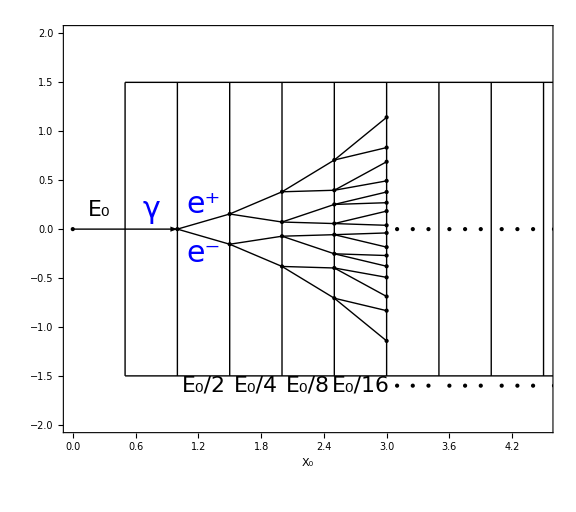

```mathematica
pts = {
{0,0},
{1,0},
pts[[2]]+RotationMatrix[Pi/10].pts[[2]]/2,pts[[2]]+RotationMatrix[-Pi/10].pts[[2]]/2,
pts[[3]]+RotationMatrix[Pi/10*1.5].pts[[2]]/2,pts[[3]]+RotationMatrix[-Pi/10*1.5].pts[[2]]/2,pts[[4]]+RotationMatrix[Pi/10*1.5].pts[[2]]/2,pts[[4]]+RotationMatrix[-Pi/10*1.5].pts[[2]]/2,
pts[[5]]+RotationMatrix[Pi/10*1.5*1.5].pts[[2]]/2,pts[[5]]+RotationMatrix[-Pi/10*1.5*1.5].pts[[2]]/2,pts[[6]]+RotationMatrix[Pi/10*1.5*1.5].pts[[2]]/2,pts[[6]]+RotationMatrix[-Pi/10*1.5*1.5].pts[[2]]/2,pts[[7]]+RotationMatrix[Pi/10*1.5*1.5].pts[[2]]/2,pts[[7]]+RotationMatrix[-Pi/10*1.5*1.5].pts[[2]]/2,pts[[8]]+RotationMatrix[Pi/10*1.5*1.5].pts[[2]]/2,pts[[8]]+RotationMatrix[-Pi/10*1.5*1.5].pts[[2]]/2,pts[[9]]+RotationMatrix[Pi/10*1.5*1.5*1.5].pts[[2]]/2,pts[[9]]+RotationMatrix[-Pi/10*1.5*1.5*1.5].pts[[2]]/2,
pts[[10]]+RotationMatrix[Pi/10*1.5*1.5*1.5].pts[[2]]/2,
pts[[10]]+RotationMatrix[-Pi/10*1.5*1.5*1.5].pts[[2]]/2,
pts[[11]]+RotationMatrix[Pi/10*1.5*1.5*1.5].pts[[2]]/2,
pts[[11]]+RotationMatrix[-Pi/10*1.5*1.5*1.5].pts[[2]]/2,
pts[[12]]+RotationMatrix[Pi/10*1.5*1.5*1.5].pts[[2]]/2,
pts[[12]]+RotationMatrix[-Pi/10*1.5*1.5*1.5].pts[[2]]/2,
pts[[13]]+RotationMatrix[Pi/10*1.5*1.5*1.5].pts[[2]]/2,
pts[[13]]+RotationMatrix[-Pi/10*1.5*1.5*1.5].pts[[2]]/2,
pts[[14]]+RotationMatrix[Pi/10*1.5*1.5*1.5].pts[[2]]/2,
pts[[14]]+RotationMatrix[-Pi/10*1.5*1.5*1.5].pts[[2]]/2,
pts[[15]]+RotationMatrix[Pi/10*1.5*1.5*1.5].pts[[2]]/2,
pts[[15]]+RotationMatrix[-Pi/10*1.5*1.5*1.5].pts[[2]]/2,
pts[[16]]+RotationMatrix[Pi/10*1.5*1.5*1.5].pts[[2]]/2,
pts[[16]]+RotationMatrix[-Pi/10*1.5*1.5*1.5].pts[[2]]/2
};
pts[[3;;4,1]]=1.5//N;
pts[[5;;8,1]]=2//N;
pts[[9;;16,1]]=2.5//N;
pts[[17;;32,1]]=3//N;

lines={Thick,
Arrow[{pts[[1]],pts[[2]]}],
Line[{pts[[2]],pts[[3]]}],
Line[{pts[[2]],pts[[4]]}],
Line[{pts[[3]],pts[[5]]}],
Line[{pts[[3]],pts[[7]]}],
Line[{pts[[4]],pts[[6]]}],
Line[{pts[[4]],pts[[8]]}],
Line[{pts[[5]],pts[[9]]}],
Line[{pts[[5]],pts[[13]]}],
Line[{pts[[6]],pts[[15]]}],
Line[{pts[[6]],pts[[14]]}],
Line[{pts[[7]],pts[[11]]}],
Line[{pts[[7]],pts[[10]]}],
Line[{pts[[8]],pts[[12]]}],
Line[{pts[[8]],pts[[16]]}],
Line[{pts[[9]],pts[[17]]}],
Line[{pts[[9]],pts[[25]]}],
Line[{pts[[13]],pts[[21]]}],
Line[{pts[[13]],pts[[19]]}],
Line[{pts[[11]],pts[[29]]}],
Line[{pts[[11]],pts[[18]]}],
Line[{pts[[10]],pts[[27]]}],
Line[{pts[[10]],pts[[23]]}],
Line[{pts[[15]],pts[[26]]}],
Line[{pts[[15]],pts[[22]]}],
Line[{pts[[14]],pts[[31]]}],
Line[{pts[[14]],pts[[20]]}],
Line[{pts[[12]],pts[[30]]}],
Line[{pts[[12]],pts[[28]]}],
Line[{pts[[16]],pts[[24]]}],
Line[{pts[[16]],pts[[32]]}]
};

frame = {
Line[{{0.5,-1.5},{5,-1.5}}],
Line[{{0.5,1.5},{5,1.5}}],
Table[Line[{{0.5+i*0.5,-1.5},{0.5+i*0.5,1.5}}],{i,0,9}]
};

dots = {
Table[Point[{{3.1+i,0},{3.25+i,0},{3.4+i,0}}],{i,0,2,0.5}],
Table[Point[{{3.1+i,-1.6},{3.25+i,-1.6},{3.4+i,-1.6}}],{i,0,2,0.5}]
};

labels = {Blue,
Text[Style["e^+",FontSize->30,FontFamily->"Palatino Linotype"],{1.25,0.25}],Text[Style["e^-",FontSize->30,FontFamily->"Palatino Linotype"],{1.25,-0.25}],
Text[Style["γ",FontSize->30,FontFamily->"Palatino Linotype"],{0.75,0.2}],Black,
Text[Style["E_0",FontSize->22,FontFamily->"Palatino Linotype"],{0.25,0.2}],
Table[Text[Style["E_0/"<>ToString[2^i],FontSize->22,FontFamily->"Palatino Linotype"],{0.75+i/2,-1.6}],{i,1,4}]
};

img = Graphics[{Point[pts],lines,frame,dots,labels},Axes->False,ImageSize->Large,AspectRatio->Automatic,Frame->{True,False,False,False},PlotRange->{{0,4.5},{-2,2}},FrameStyle->Directive[Black,Large],FrameLabel->{"X_0",""}]
```

```mathematica
pts = {
{0,0},
{1,0},
pts[[2]]+RotationMatrix[Pi/10].pts[[2]]/2
}
```

{{0,0},{1,0},{1+1/4 √(1/2 (5+√5)),1/8 (-1+√5)}}

## CP skice posamezno

```mathematica
a0 = {0,0};
a1={1.2,0};
fi=50*Pi/180;
a2 =RotationMatrix[fi].{1/√2,0}//N;
a3 =RotationMatrix[-fi].{1/√2,0}//N;

text = {"A_1","A_2","A",OverBar["A_2"],OverBar["A "]};
graph={{Black,Arrow[{a0,a1}],Black,Dotted,Line[{a1,1.7a1}]},{Black,Arrow[{a1,a1+a2}],Black,Dotted,Line[{a1,a1+1.5a2}]},{Blue,Thick,Arrow[{a0,a1+a2}]},{Dashed,Black,Arrow[{a1,a1+a3}]},{Red,Thick,Arrow[{a0,a1+a3}]}};
gtext[j_]:=Table[{Black,Text[Style[text[[i]],FontSize->22],points[[i]]]},{i,1,j}];
symtext={{Text[Style["ϕ",FontSize->22],{1.347,0.06244}],Circle[a1,0.25,{0,fi}]},{},{Text[Style["-ϕ",FontSize->22],{1.35,-0.1}],Circle[a1,0.28,{-fi,0}]},{Text[Style["|A| = |Ā|",FontSize->30],{0.4,0.5}]}};
points={{0.7151,0.04766},{1.31,0.2398},{0.8592,0.3396},{1.5,-0.2591},{0.6892,-0.3367}};

Table[Graphics[{graph[[1;;n]],gtext[n],symtext[[1;;n-1]]},ImageSize->Large,PlotRange->{{0,1.8},{-0.6,0.7}}],{n,1,5}]//Column;
```

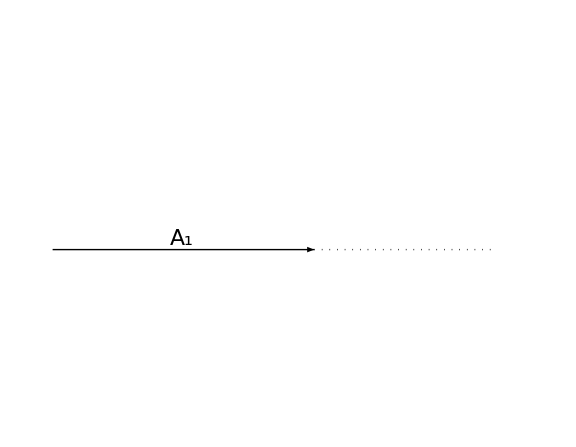
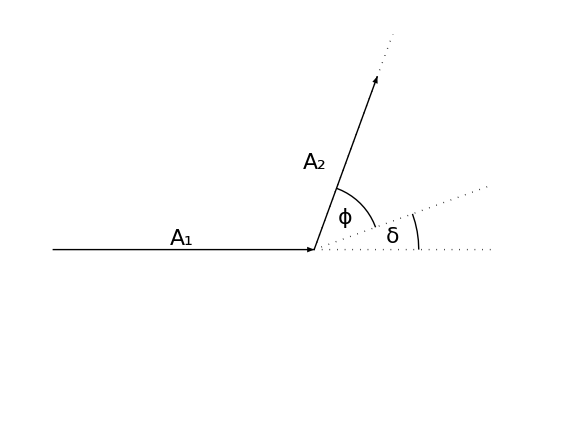
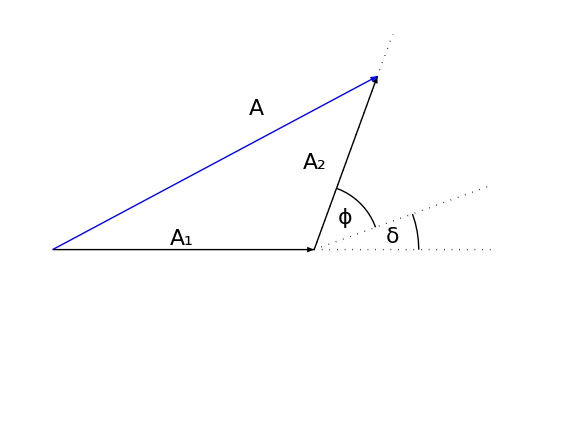
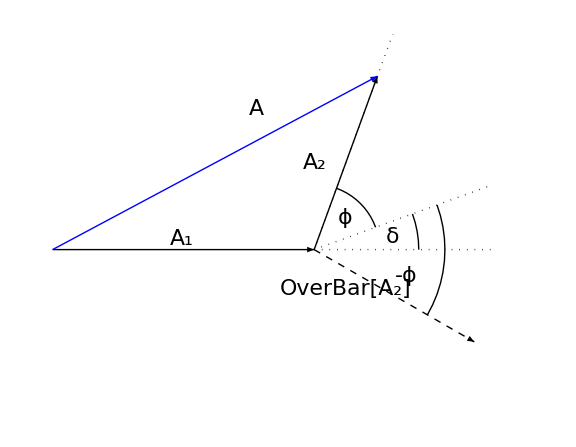
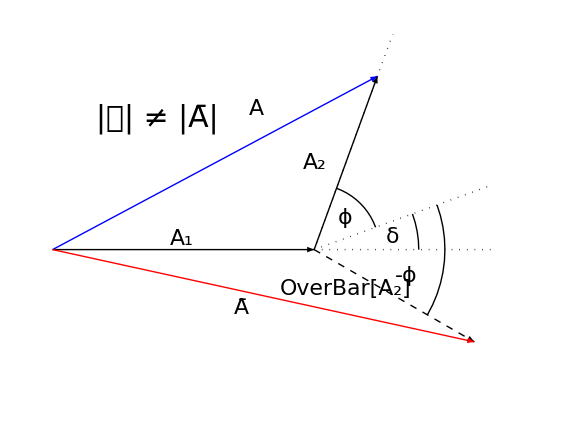

```mathematica
a0 = {0,0};
a1={1,0};
fi=50*Pi/180;
delta = 20*Pi/180;
a2 =RotationMatrix[fi].RotationMatrix[delta].{1/√2,0}//N;
a3 =RotationMatrix[-fi].RotationMatrix[delta].{1/√2,0}//N;

text = {"A_1","A_2","A",OverBar["A_2"],OverBar["A "]};
graph={{Black,Arrow[{a0,a1}],Black,Dotted,Line[{a1,1.7a1}]},{Black,Arrow[{a1,a1+a2}],Black,Dotted,Line[{a1,a1+RotationMatrix[delta].{1/√2,0}}],Line[{a1,a1+1.5a2}]},{Blue,Thick,Arrow[{a0,a1+a2}]},{Dashed,Black,Arrow[{a1,a1+a3}]},{Red,Thick,Arrow[{a0,a1+a3}]}};
symtext={{Text[Style["δ",FontSize->22,FontFamily->"Palatino Linotype"],{1.3,0.05}],Circle[a1,0.4,{0,delta}],Text[Style["ϕ",FontSize->22,FontFamily->"Palatino Linotype"],{1.12,0.12}],Circle[a1,0.25,{delta,delta+fi}]},{},{Text[Style["-ϕ",FontSize->22,FontFamily->"Palatino Linotype"],{1.35,-0.1}],Circle[a1,0.5,{delta,delta-fi}]},{Text[Style["|𝒜| ≠ |Ā|",FontSize->30,FontFamily->"Palatino Linotype"],{0.4,0.5}]}};
points={{0.4943,0.03913},{1.002,0.3317},{0.7776,0.538},{1.12,-0.15},{0.7222,-0.2226}};

img=Table[Graphics[{graph[[1;;n]],gtext[n],symtext[[1;;n-1]]},ImageSize->Large,PlotRange->{{0,1.8},{-0.6,0.8}}],{n,1,5}]
```

```mathematica
Table[Export["D:\\Faks\\5. letnik\\Magisterij\\slike\\amp2_"<>ToString[i]<>".pdf",img[[i]]],{i,1,Length[img]}]
```

{D:\Faks\5. letnik\Magisterij\slike\amp2_1.pdf,D:\Faks\5. letnik\Magisterij\slike\amp2_2.pdf,D:\Faks\5. letnik\Magisterij\slike\amp2_3.pdf,D:\Faks\5. letnik\Magisterij\slike\amp2_4.pdf,D:\Faks\5. letnik\Magisterij\slike\amp2_5.pdf}

## CKM

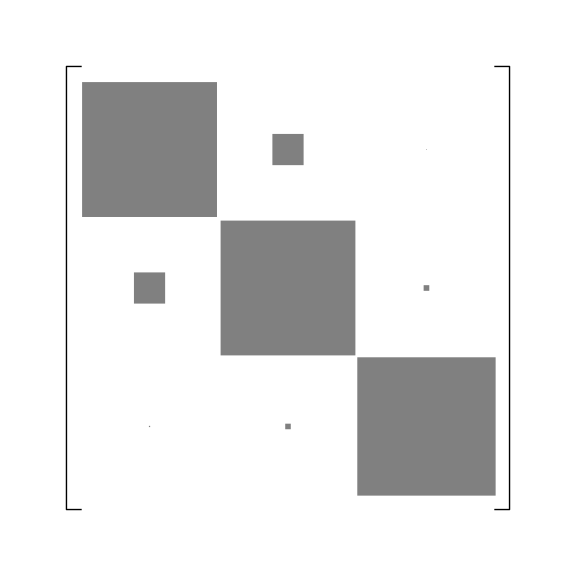

```mathematica
centers={{0.5,2.5},{1.5,2.5},{2.5,2.5},{0.5,1.5},{1.5,1.5},{2.5,1.5},{0.5,0.5},{1.5,0.5},{2.5,0.5}};
V={0.97427,0.2254,0.005,0.2252,0.97346,0.0408,0.009,0.0401,0.999146};
Graphics[{Thick,Black,Line[{{0.01,-0.1},{-0.1,-0.1},{-0.1,3.1},{0.01,3.1}}],Line[{{3-0.01,-0.1},{3.1,-0.1},{3.1,3.1},{3-0.01,3.1}}],Table[{Gray,Rectangle[centers[[i]]-{1,1}*0.5*V[[i]],centers[[i]]+{1,1}*0.5*V[[i]]]},{i,1,9}]},PlotRange->{{-0.2,3.2},{-0.2,3.2}},FrameTicks->False,ImageSize->Large]
```

## CP symmetry

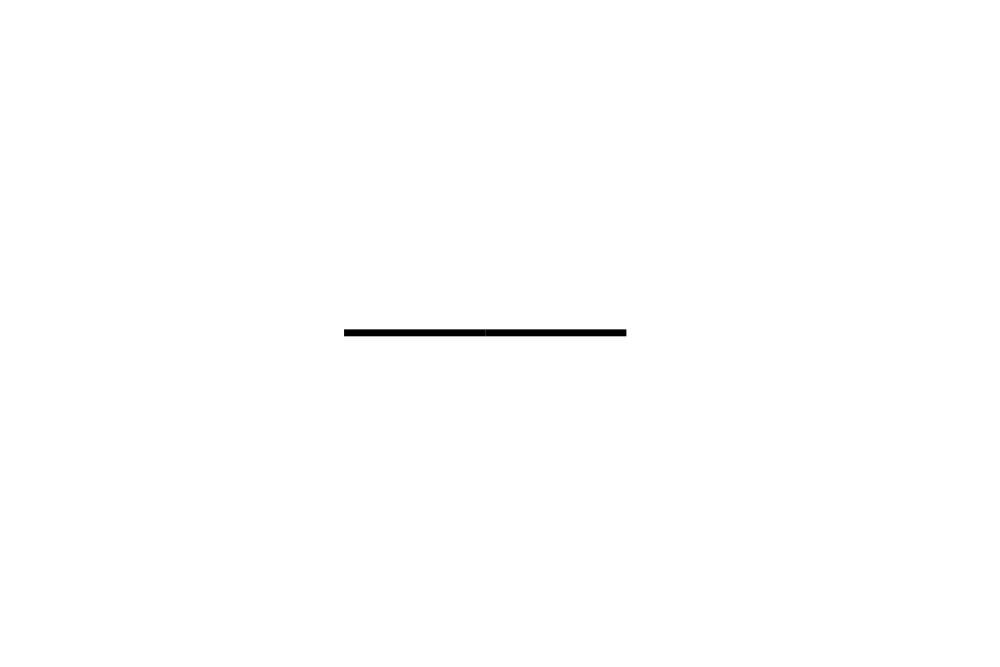
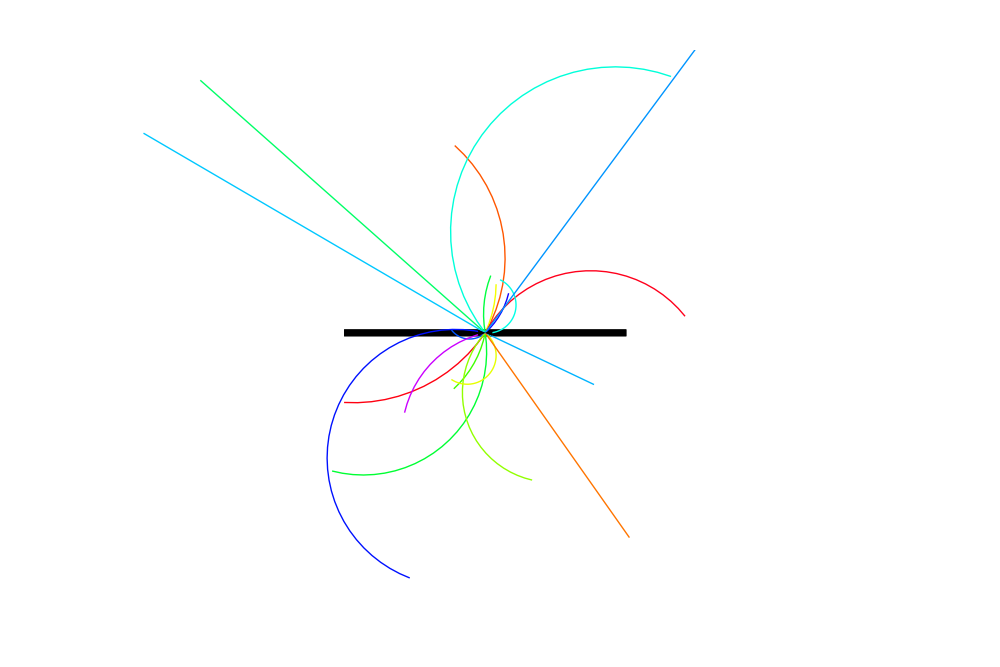
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
x1=0.5;
x2=2;
x3=3.5;
sp = 0.15;
sp1 = 0.05;
sp2 = 0.1;
x=Table[{3.5,0}+RandomReal[1.5{-1,1},2],{i,1,15}];
angle=Pi+Table[ArcTan[x[[i,1]]-7/2,x[[i,2]]],{i,1,Length[x]}];
plotR[r_,fi_, thickness_, col_]:={col,Rotate[Rectangle[{3.5,0}+RotationMatrix[fi].{0,r}+{-0.4,-thickness},{3.5,0}+RotationMatrix[fi].{0,r}+{0.4,thickness}],fi]};

evtgen = {White,EdgeForm[{Black,Thick}],Rectangle[{-0.5,-0.5},{0.5,0.5}]};
transformations={Gray,Arrowheads[.04],Thickness[0.01],Arrow[{{1.25,0},{1.85,0}}]};
arrows = {Thickness[0.005],Arrowheads[.03],Arrow[{{2,0},{3.5,0}}],Arrow[{{5,0},{3.5,0}}]};
colision = {Table[{Hue[RandomReal[]],Circle[x[[l]],Norm[x[[l]]-{3.5,0}],{angle[[l]],angle[[l]]+Pi*RandomReal[{-1,1}]}]},{l,1,Length[x]}],
Table[{Hue[RandomReal[]],Line[{{3.5,0},{3.5,0}+RandomReal[4{-1,1},2]}]},{i,1,5}]
};
detector = {
Table[plotR[1.5,fi,0.2,Magenta],{fi,0,2Pi-2Pi/10,2Pi/10}],
Table[plotR[0.5,fi,0.02, Red],{fi,0,2Pi-2Pi/6,2Pi/6}],
Table[plotR[2.5,fi,0.4, Orange],{fi,0,2Pi-2Pi/30,2Pi/30}]
};
text = {Text[Style["EvtGen",FontSize->22,FontFamily->"Palatino Linotype"],{0,0}]};
reconstruction={Text[Style["# create final state particle lists
selectParticle('K-', '', True, myMain)
selectParticle('pi+', '', True, myMain)
selectParticle('pi-', '', True, myMain)
selectParticle('e+', '', True, myMain)
selectParticle('gamma', '', True, myMain)
# reconstruct pi0 -> gamma gamma decay
reconstructDecay('pi0 -> gamma gamma', 
	'0.05 < M < 1.7', 1, True, myMain)
reconstruct D0 -> K- pi+ decay (and c.c.)
reconstructDecay('D0 -> K- pi+', 
	'1.800 < M < 1.900', 1, True, myMain)",FontFamily->"Courier",TextAlignment->Left,FontSize->15],{9,0}]};

timed = {arrows, colision,detector};

exp=Table[Graphics[Table[timed[[1;;i]],{i,1,n}],PlotRange->{{-0.686,8},{-2.904,2.89}},Axes->False,ImageSize->1000,AspectRatio->Automatic,PlotRange->{{-5,5},{-5,5}}],{n,1,Length[timed]}]
```

```mathematica
Table[Export["/home/mlubej/work/BNote/fig/sim_"<>ToString[i]<>".pdf",exp[[i]]],{i,1,Length[exp]}]
```

{/home/mlubej/work/BNote/fig/sim_1.pdf,/home/mlubej/work/BNote/fig/sim_2.pdf,/home/mlubej/work/BNote/fig/sim_3.pdf}

## Rekonstrukcija

```mathematica
s1= {};
s2 = s1;
s3 = s1;
s4 = s1;
s5=s1;
n = 200;

For[x=-5,x<=5,x++,{
For[y=-5,y<=5,y++,{
If[(x/5)^2+(y/5)^2+RandomReal[{-0.1,0.1}]<1,AppendTo[s1,{ColorData[{"Rainbow","Reverse"}][(x/5)^2+(y/5)^2+RandomReal[{-0.2,0.2}]],Rectangle[{x,y}/10,{x,y}/10+{0.09,0.09},RoundingRadius->0.02]}]];
}];
}];

For[x=-5,x<=5,x++,{
For[y=-5,y<=5,y++,{
If[(x/5)^2+(y/5)^2+RandomReal[{-0.1,0.1}]<1,AppendTo[s2,{ColorData[{"Rainbow","Reverse"}][(x/5)^2+(y/5)^2+RandomReal[{-0.2,0.2}]],Rectangle[{3,1}+{x,y}/10,{3,1}+{x,y}/10+{0.09,0.09},RoundingRadius->0.02]}]];
}];
}];

For[x=-5,x<=5,x++,{
For[y=-5,y<=5,y++,{
If[(x/5)^2+(y/5)^2+RandomReal[{-0.1,0.1}]<1,AppendTo[s3,{ColorData[{"Rainbow","Reverse"}][(x/5)^2+(y/5)^2+RandomReal[{-0.2,0.2}]],Rectangle[{7,-0.5}+{x,y}/10,{7,-0.5}+{x,y}/10+{0.09,0.09},RoundingRadius->0.02]}]];
}];
}];

For[x=-5,x<=5,x++,{
For[y=-5,y<=5,y++,{
If[(x/5)^2+(y/5)^2+RandomReal[{-0.1,0.1}]<1,AppendTo[s4,{ColorData[{"Rainbow","Reverse"}][(x/5)^2+(y/5)^2+RandomReal[{-0.2,0.2}]],Rectangle[{13,-1}+{x,y}/10,{13,-1}+{x,y}/10+{0.09,0.09},RoundingRadius->0.02]}]];
}];
}];

For[x=-10,x≤10,x++,{
For[y=-10,y≤10,y++,{
If[(x/10)^2+(y/10)^2+RandomReal[2{-0.1,0.1}]<1,AppendTo[s5,{ColorData[{"Rainbow","Reverse"}][(x/10)^2+(y/10)^2+RandomReal[{-0.2,0.2}]],Rectangle[{10,2.5}+{x,y}/10,{10,2.5}+{x,y}/10+{0.09,0.09},RoundingRadius->0.02]}]];
}];
}];
```

```mathematica
Clear[particles1,particles2,particles3]
```

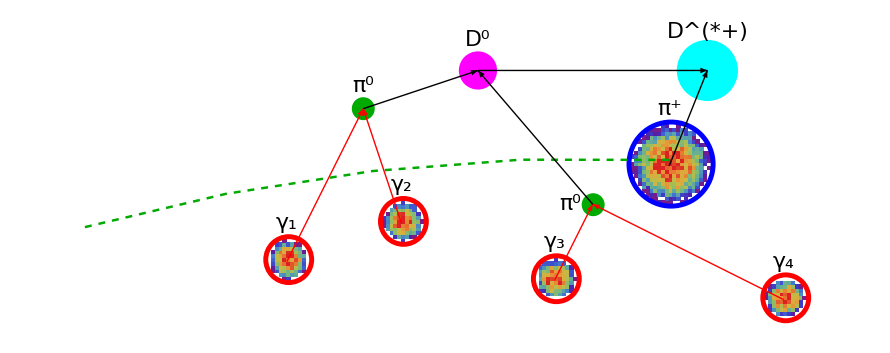

```mathematica
clusters = {s1,s2,s3,s4,s5};
fsp = {Red,Thickness[0.004],Circle[{0.05,0.05},0.6],Circle[{3.05,1.05},0.6],Circle[{7.05,-0.5+0.05},0.6],Circle[{13.05,-1+0.05},0.6],Blue,Circle[{10.05,2.55},1.1]};
textfsp = {Text[Style["γ_1",FontSize->22,FontFamily->"Palatino Linotype"],{0,1}],Text[Style["γ_2",FontSize->22,FontFamily->"Palatino Linotype"],{3,2}],Text[Style["γ_3",FontSize->22,FontFamily->"Palatino Linotype"],{7,0.5}],Text[Style["γ_4",FontSize->22,FontFamily->"Palatino Linotype"],{13,0}],Text[Style["π^+",FontSize->22,FontFamily->"Palatino Linotype"],{10,4}]};
track = {Darker[Green],Dashed,Thickness[0.002],Circle[{8,-47.3},50,{Pi/2-0.04,Pi-1.3}]};

particles1[x_]:= {{Darker[Green],Disk[{2,4},0.3],Disk[{8,1.5},0.3]},
{If[x == 3,Red,Black],Arrowheads[0.03],Arrow[{{0,0},{2,4}}],Arrow[{{3,1},{2,4}}],Arrow[{{7,-0.5},{8,1.5}}],Arrow[{{13,-1},{8,1.5}}]},
{Text[Style["π^0",FontSize->22,FontFamily->"Palatino Linotype"],{2,4+0.6}],Text[Style["π^0",FontSize->22,FontFamily->"Palatino Linotype"],{7.4,1.5}]}
};

particles2[x_]:= {{Magenta,Disk[{5,5},0.5]},
{If[x == 4,Red,Black],Arrowheads[0.03],Arrow[{{2,4},{5,5}}],Arrow[{{8,1.5},{5,5}}]},
{Text[Style["D^0",FontSize->22,FontFamily->"Palatino Linotype"],{5,5+0.8}]}
};

particles3[x_]:= {{Cyan,Disk[{11,5},0.8]},
{If[x == 5,Red,Black],Arrowheads[0.03],Arrow[{{5,5},{11,5}}],Arrow[{{10,2.5},{11,5}}]},
{Text[Style["D^(*+)",FontSize->22,FontFamily->"Palatino Linotype"],{11,6}]}
};

frame[i_]:={{clusters,track},{fsp,textfsp},particles1[i],particles2[i],particles3[i]}
Graphics[{clusters,fsp,textfsp,track,particles1[3],particles2[3],particles3[3]}]
img = Table[Graphics[frame[i][[1;;i]],ImageSize->1000,PlotRange->{{-5.75,14},{-1.9,6.3}}],{i,1,5}];
```

```mathematica
Table[Export["D:\\Faks\\5. letnik\\Magisterij\\slike\\recon_"<>ToString[i]<>".pdf",img[[i]]],{i,1,Length[img]}]
```

{D:\Faks\5. letnik\Magisterij\slike\recon_1.pdf,D:\Faks\5. letnik\Magisterij\slike\recon_2.pdf,D:\Faks\5. letnik\Magisterij\slike\recon_3.pdf,D:\Faks\5. letnik\Magisterij\slike\recon_4.pdf,D:\Faks\5. letnik\Magisterij\slike\recon_5.pdf}

## merged

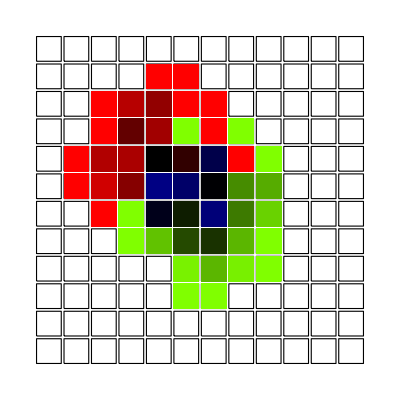

```mathematica
s1= {};
s2=s1;
s3 = s1;
grid = s1;

For[x=-4,x≤7,x++,{
For[y=-7,y≤4,y++,{
AppendTo[grid,{White,EdgeForm[Black],Rectangle[{x,y}/10,{x,y}/10+{0.09,0.09},RoundingRadius->0.02]}];
}];
}];

For[x=-3,x≤3,x++,{
For[y=-3,y≤3,y++,{
If[(x/3)^2+(y/3)^2+RandomReal[5{-0.1,0.1}]<1,AppendTo[s1,{Hue[1,1,((x/3)^2+(y/3)^2+RandomReal[{-0.3,0.3}])+0.3],Rectangle[{x,y}/10.,{x,y}/10+{0.09,0.09},RoundingRadius->0.02]}]];
}];
}];

For[x=-3,x≤3,x++,{
For[y=-3,y≤3,y++,{
If[(x/3)^2+(y/3)^2+RandomReal[5{-0.1,0.1}]<1,AppendTo[s2,{Hue[1/4,1,((x/3)^2+(y/3)^2+RandomReal[{-0.3,0.3}])+0.3],Rectangle[{0.2,-0.2}+{x,y}/10,{0.2,-0.2}+{x,y}/10+{0.09,0.09},RoundingRadius->0.02]}]];
}];
}];

s3t = Intersection[s1[[;;,2]],s2[[;;,2]]];

For[i =1,i<Length[s3t],i++,{
AppendTo[s3,{Hue[2/3,1,((s3t[[i,1,1]]/3)^2+(s3t[[i,1,2]]/3)^2+RandomReal[{-0.3,0.3}])+0.3],s3t[[i]]}];
}];



Graphics[{grid,s1,s2,s3}]
```

```mathematica
s3t[[1]]
```

Rectangle[{0.,-0.2},{0.09,-0.11},RoundingRadius→0.02]

```mathematica
s3
```

{{Hue[2/3,1,0.52002+1/9 Rectangle[{0.,-0.2},{0.09,-0.11},RoundingRadius→0.02]^2],{0.09,-0.11}},{Hue[2/3,1,0.257545+1/9 Rectangle[{0.,-0.1},{0.09,-0.01},RoundingRadius→0.02]^2],{0.09,-0.01}},{Hue[2/3,1,0.568068+1/9 Rectangle[{0.,0.},{0.09,0.09},RoundingRadius→0.02]^2],{0.09,0.09}},{Hue[2/3,1,0.213618+1/9 Rectangle[{0.1,-0.2},{0.19,-0.11},RoundingRadius→0.02]^2],{0.19,-0.11}},{Hue[2/3,1,0.56336+1/9 Rectangle[{0.1,-0.1},{0.19,-0.01},RoundingRadius→0.02]^2],{0.19,-0.01}},{Hue[2/3,1,0.323153+1/9 Rectangle[{0.1,0.},{0.19,0.09},RoundingRadius→0.02]^2],{0.19,0.09}},{Hue[2/3,1,0.391119+1/9 Rectangle[{0.2,0.},{0.29,0.09},RoundingRadius→0.02]^2],{0.29,0.09}}}